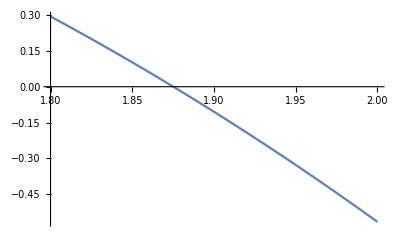

```mathematica
f=Cosh[x]Cos[x]+1;
Plot[f,{x,1.8,2.0}]
```

```mathematica
ϕ=ArcCos[-1/Cosh[x]];
Dϕ=D[ϕ,x]
```

-(Sech[x] Tanh[x])/(√(1-Sech[x]^2))

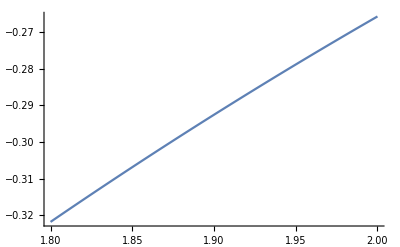

```mathematica
Plot[Dϕ,{x,1.8,2.0}]
```

```mathematica
ϵ=10^-6;
q=0.32;
ϵ1=ϵ(1-q)/q;
x0=1.8
```

1.8

```mathematica
x1=ϕ/.x->x0;
NumberForm[x1,9]
Abs[x1-x0]<ϵ1
x0=x1;
```

1.87510362

True

```mathematica
f/.x->x0
```

-0.999998

```mathematica
Df=D[f,x]
x0=1.8
```

-Cosh[x] Sin[x]+Cos[x] Sinh[x]

1.8

```mathematica
f0=f/.x->x0;
Df0=Df/.x->x0;
x1=x0-f0/Df0;
NumberForm[x1,9]
Abs[x1-x0]<ϵ
x0=x1;
```

1.87510407

True

```mathematica
f/.x->x0
```

-5.14679×10^-12